```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=ReplacePart[0*IdentityMatrix[m],Join[Table[{x,x+1},{x,Range[1,m,4]}],Table[{x,x-1},{x,Range[4,m,4]}]]->t]
```

```mathematica
Clear[leadgenerateleft]
```

```mathematica
leadgenerateleft[ω_,δ_,t_,ϵ_,m_]:= leadgenerateleft[ω,δ,t,ϵ,m]= Module[{unit=Inverse[β[ω,δ,t,ϵ,m]],J=Inverse[β[ω,δ,t,ϵ,m]]},Do[J= Inverse[IdentityMatrix[m]-unit.T[t,m].J.ConjugateTranspose[T[t,m]]].unit,25000];J=J]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-Inverse[β[ω,δ,t,ϵ,m]].T[t,m].leadgenerateleft[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-Inverse[β[ω,δ,t,ϵ,m]].T[t,m].leadgenerateleft[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter2/dos/Re_zgnr_lead.dat",Table[{ω,Re[Tr[SL[ω,0.0001,1,0,6]]]/π},{ω,Range[-4,4,0.01]}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter2/dos/Re_zgnr_lead.dat

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:= Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].SL[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]]-T[t,m].GNON[ω,δ,t,ϵ,m].ConjugateTranspose[T[t,m]].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr1[0.1,0.0001,1,0,8]
```

1.

```mathematica
Monitor[Table[{ω,If[tr1[ω,0.0001,1,0,6]>tr1[1.03,0.0001,1,0,6],tr1[1.03,0.0001,1,0,6],tr1[ω,0.0001,1,0,6]]},{ω,Range[-4,4,0.01]}],ω]
```

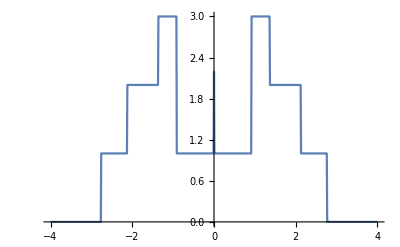

```mathematica
ListPlot[%49,Joined->True]
```

```mathematica
Export["~/Desktop/Thesis/thesis26jun/Images/Chapter2/zgnr_6_transm.dat",Table[{ω,},{ω,Range[-4,4,0.01]}]]
```

~/Desktop/Thesis/thesis26jun/Images/Chapter2/zgnr_6_transm.dat

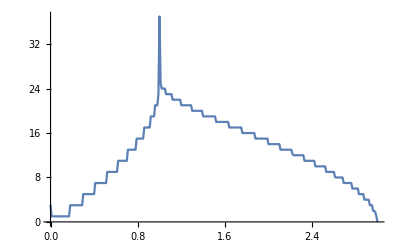

```mathematica
ListPlot[%27,Joined->True]
```

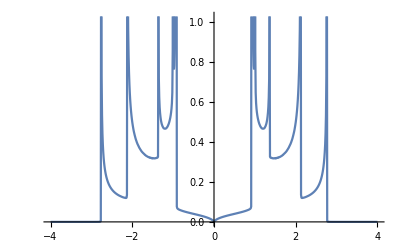

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,6][[2,2]]]},{ω,Range[-4,4,0.01]}]]
```

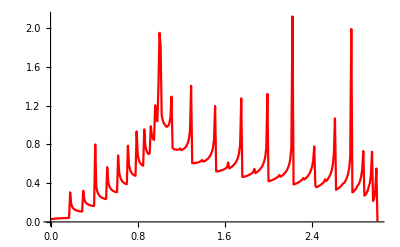

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,50][[25,25]]]},{ω,Range[0,3,0.01]}],PlotStyle->Red,PlotRange->All]
```

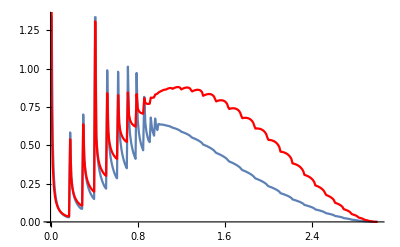

```mathematica
Show[%30,%32]
```

```mathematica
Table[Export["/home/shardulmukim/PhD/fwi/zgnr/50zgnr/leads/lead_"<>ToString[ω]<>".dat",leadgenerateleft[ω,0.0001,1,0,50]],{ω,Range[0,3,0.01]}]
```

```mathematica
leads= Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/51AGNR/lead"<>ToString[X]<>".dat"]],{X,Range[0.1,3,0.01]}]
```

{{{-0.0844331-0.00106503 ⅈ,-0.599711-0.00950359 ⅈ,0.024463+0.0000546985 ⅈ,0.264531+0.00968055 ⅈ,95,0.337626-0.000169041 ⅈ,0.0435589+0.00196302 ⅈ,-0.408733+0.00938864 ⅈ},{1},98,{1},{1}},289,{1}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=leads[[Round[ω*100]]]
```

```mathematica
LEFT[1,0.0001,1,0]//Dimensions
```

{102,102}

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ].ρ[t,m].LEFT[ω,δ,t,ϵ].ρ[t,m]].LEFT[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-LEFT[ω,δ,t,ϵ,m].ρ[t,m].LEFT[ω,δ,t,ϵ,m].ρ[t,m]].LEFT[ω,δ,t,ϵ,m]
```

```mathematica
ListLinePlot[Table[{ω,-Im[IL[ω,0.0001,1,0,51][[51,51]]]},{ω,Range[0.01,2.9,0.01]}]]
```

Part::partw: Part 51 of Dot[<<10743561640 bytes>>] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Clear[SL]
```